```mathematica
f[x_]=(x-√ArcTan[2x])/(1+4x^2)
```

(x-√ArcTan[2 x])/(1+4 x^2)

```mathematica
Integrate[f[x],x]
```

-1/3 ArcTan[2 x]^(3/2)+1/8 Log[1+4 x^2]

```mathematica
Integrate[f[x],{x,0,1}]
```

-1/3 ArcTan[2]^(3/2)+Log[5]/8

```mathematica
N[-1/3 ArcTan[2]^(3/2)+Log[5]/8]
```

-0.187138

```mathematica
f[x_]=Sin[x]/x
```

Sin[x]/x

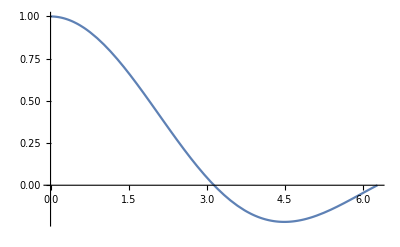

```mathematica
Plot[f[x],{x,0,2Pi}]
```

```mathematica
Solve[f[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{}

```mathematica
Abs[Integrate[f[x],{x,0,Pi}]]+Abs[Integrate[f[x],{x,Pi,2Pi}]]
```

2 SinIntegral[π]-SinIntegral[2 π]

```mathematica
N[2 SinIntegral[π]-SinIntegral[2 π]]
```

2.28572

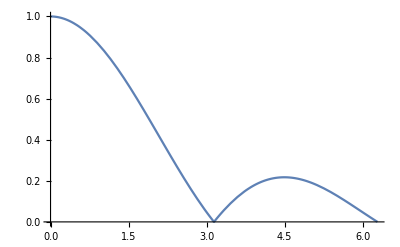

```mathematica
Plot[Abs[f[x]],{x,0,2Pi}]
```

```mathematica
f[x_]=x^3
```

x^3

```mathematica
g[x_]=2x+1
```

1+2 x

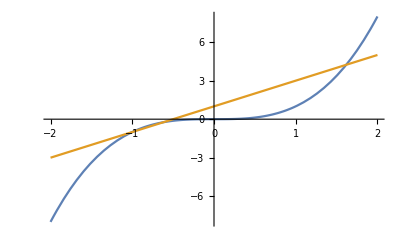

```mathematica
Plot[{f[x],g[x]},{x,-2,2}]
```

```mathematica
Solve[f[x]==g[x],x]
```

{{x→-1},{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
Abs[Integrate[f[x]-g[x],{x,-1,1/2 (1-√5)}]]+Abs[Integrate[f[x]-g[x],{x,1/2 (1-√5),1/2 (1+√5)}]]
```

-9/4+√5+1/32 (1-√5)^4+1/2 (1+√5)-1/64 (1+√5)^4-2 (-1/2+1/8 (1-√5)^2)+2 (-1/8 (1-√5)^2+1/8 (1+√5)^2)

```mathematica
Simplify[%]
```

1/8 (-11+15 √5)

```mathematica
N[1/8 (-11+15 √5)]
```

2.81763

```mathematica
f[x_]=Cos[x]/(x+1)
```

Cos[x]/(1+x)

```mathematica
NIntegrate[f[x],{x,0,1}]
```

0.601044

```mathematica
Trapezis[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+2*Sum[f[a+k*h],{k,1,n-1}]+f[b])*h/2,20]]
```

```mathematica
Trapezis[f,{0,1,10}]
```

0.60141412919716912939

```mathematica
f''[x]
```

(2 Cos[x])/(1+x)^3-Cos[x]/(1+x)+(2 Sin[x])/(1+x)^2

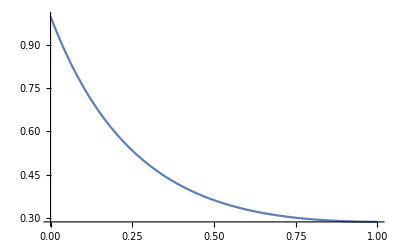

```mathematica
Plot[Abs[f''[x]],{x,0,1}]
```

```mathematica
1/(12*10^2)
```

1/1200

```mathematica
N[%]
```

0.000833333

```mathematica
Simpson[f_,{a_,b_,n_}]:=Module[{h},
h=(b-a)/n;
N[(f[a]+4*Sum[f[a+(2*k+1)*h],{k,0,n/2-1}]+2*Sum[f[a+2*k*h],{k,1,n/2-1}]+f[b])*h/3,20] ]
```

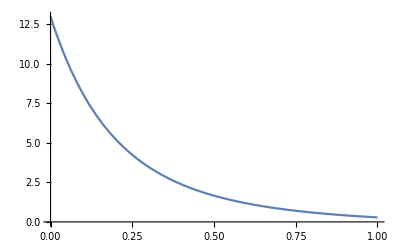

```mathematica
Plot[Abs[f''''[x]],{x,0,1}]
```

```mathematica
Abs[f''''[0]]
```

13

```mathematica
1/(180*10^4)
```

1/1800000

```mathematica
N[%]
```

5.55556×10^-7

```mathematica
NumberForm[5.555555555555555*^-7,16]
```

5.555555555555555×10^-7